```mathematica
SetDirectory[NotebookDirectory[]];
```

## Importing data

```mathematica
AllScatAng = Flatten[Import["AllScatterAnglesSecBeam.dat"]];
SelectScatAng =Flatten[Import["ScatterAnglesSelected.dat"]];
AnglesTarget = Flatten[Import["anglesOnTarget.dat"]];
AllSecEnergies = Flatten[Import["AllSecundaryBeamEnergies.dat"]];
PriBeamEnegies = Flatten[Import["PrimaryBeamEnergies.dat"]];
SecBeamEnergiesSelect = Flatten[Import["SecundaryBeamEnergiesSelected.dat"]];
SecBeamEnergyTarget = Flatten[Import["SecundaryBeamEnergyOnTarget.dat"]];
ReactionPoints = Import["ReactionPoints.dat"];
PointsOnTarget = Import["Points_on_Target.dat"];
Trajectories3D=Import["rays3Dplot.dat"];
```

## Energies

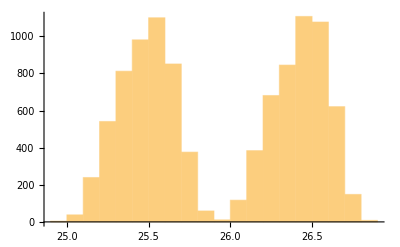

```mathematica
Histogram[AllSecEnergies,20]
```

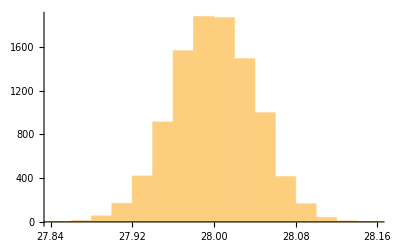

```mathematica
Histogram[PriBeamEnegies,20]
```

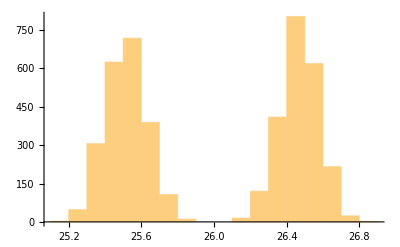

```mathematica
Histogram[SecBeamEnergiesSelect,20]
```

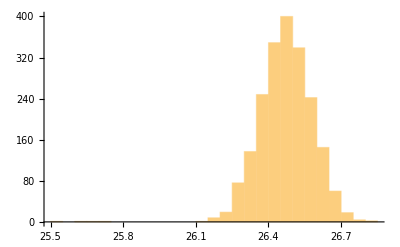

```mathematica
Histogram[SecBeamEnergyTarget,20]
```

## Angles

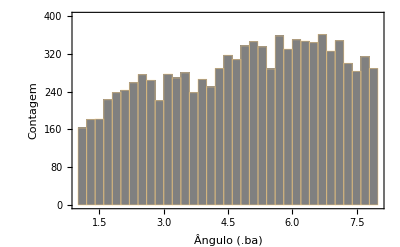

```mathematica
Histogram[Style[AllScatAng,Gray],25, Frame->True,FrameStyle->Directive[Black,Bold,14],PlotRange->{{1,8},{0,400}},FrameLabel->{Style["Ângulo (.ba)",Black,14],Style["Contagem",Black,14]}]
```

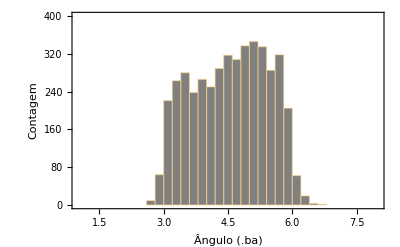

```mathematica
Histogram[Style[SelectScatAng,Gray],20, Frame->True,FrameStyle->Directive[Black,Bold,14],PlotRange->{{1,8},{0,400}},FrameLabel->{Style["Ângulo (.ba)",Black,14],Style["Contagem",Black,14]}]
```

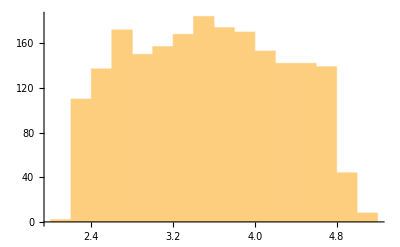

```mathematica
Histogram[AnglesTarget,20]
```

## Reaction Points on primary target and points on target

```mathematica
ListPointPlot3D[ReactionPoints]
```

-Graphics3D-

```mathematica
ListPointPlot3D[PointsOnTarget]
```

-Graphics3D-

# 3D trajectiories

```mathematica
pos=Join[{1},Flatten[Position[Trajectories3D,{"&"}]]];
```

```mathematica
plot3D=Table[Trajectories3D[[pos[[i]];;pos[[i+1]]-1]],{i,1,Length[pos]-1}];
```

```mathematica
block2=Partition[Flatten[Table[{{2.45,0.01*Cos[θ*Pi/180],0.01*Sin[θ*Pi/180]},{2.45,0,0}},{θ,0,360}]],3];
```

```mathematica
col2=Partition[Flatten[Table[{{2.238,0.03*Cos[θ*Pi/180],0.03*Sin[θ*Pi/180]},{2.238,0.15*Cos[θ*Pi/180],0.15*Sin[θ*Pi/180]}},{θ,0,360}]],3];
```

```mathematica
col1=Partition[Flatten[Table[{{0.204,0.02125*Cos[θ*Pi/180],0.02125*Sin[θ*Pi/180]},{0.204,0.15*Cos[θ*Pi/180],0.15*Sin[θ*Pi/180]}},{θ,0,360}]],3];
```

```mathematica
grafico=Show[
Table[ListLinePlot3D[plot3D[[i]],PlotRange->{{-0.0,3},{-0.15,0.15},{-0.15,0.15}},PlotStyle->Directive[Black,Thin],AxesLabel->{Style["z[m]",20,Black],Style["x[m]",20,Black],Style["y[m]",20,Black]},
AxesStyle->Directive[Black,14]],{i,1,60,2}],
Table[ListLinePlot3D[plot3D[[i]],PlotRange->{{-0.0,3},{-0.15,0.15},{-0.15,0.15}},PlotStyle->Directive[Red,Thin]],{i,2,60,2}],
ListLinePlot3D[col2,PlotStyle->Green,PlotLabels->Callout[Style["Colimador 2",Orange,30],{2.55,0.08,0.08},LabelStyle->"Medium"]],
ListLinePlot3D[col1,PlotStyle->Green,PlotLabels->Callout[Style["Colimador 1",Orange,30],{0.8,0.08,0.08},LabelStyle->"Medium"]],
ListLinePlot3D[block2,PlotStyle->Blue,PlotLabels->Callout[Style["Bloqueador",Orange,30],{2.85,-0.08,-0.08},LabelStyle->"Medium"]],
BoxRatios->{5, 1, 1}]
```

-Graphics3D-

```mathematica
grafico=Show[
Table[ListLinePlot3D[plot3D[[i]],PlotRange->{{-0.0,3},{-0.15,0.15},{-0.15,0.15}},PlotStyle->Directive[Black,Thin],AxesLabel->{Style["z[m]",20,Black],Style["x[m]",20,Black],Style["y[m]",20,Black]},
AxesStyle->Directive[Black,14]],{i,1,60,2}],
Table[ListLinePlot3D[plot3D[[i]],PlotRange->{{-0.0,3},{-0.15,0.15},{-0.15,0.15}},PlotStyle->Directive[Red,Thin]],{i,2,60,2}],
ListLinePlot3D[col2,PlotStyle->Green,PlotLabels->Callout[Style["Colimador 2",Orange,30],{2.55,0.08,0.08},LabelStyle->"Medium"]],
ListLinePlot3D[col1,PlotStyle->Green,PlotLabels->Callout[Style["Colimador 1",Orange,30],{0.8,0.08,0.08},LabelStyle->"Medium"]],
BoxRatios->{5, 1, 1}]
```

-Graphics3D-

-Graphics3D-